# Systems of Differential Equations

## Using a Change of Variables and Nullclines to analyze systems

Considering a system of differential equations of the form:
ẋ = 1/2(x-x^3) - y-1/2 x y^2
ẏ = x -1/2 x^2 y+ 1/2 y - 1/2 y^3

Here, we would like to determine how solutions behave by investigating regions of the phase-plane.

## Define the functions

```mathematica
f[x_,y_] = 1/2 x - y - 1/2(x^3+x y^2);
g[x_,y_] = x + 1/2 y - 1/2(y^3+x^2 y);
```

Now, let’s define the vec

```mathematica
F[x_,y_] = {f[x,y],g[x,y]};
```

(x/2-y+1/2 (-x^3-x y^2)
x+y/2+1/2 (-x^2 y-y^3))

## Step 1: Find the “Easy” Solutions (Equilibrium Points)

```mathematica
eqPts = Solve[F[x,y]=={0,0},{x,y}]
```

{{x→0,y→0}}

## Step 2: Linearize about the Equilibrium Points

Let’s first determine the Jacobian.

```mathematica
Df = Grad[F[x,y],{x,y}];
Df//MatrixForm
```

(1/2+1/2 (-3 x^2-y^2) | -1-x y
1-x y | 1/2+1/2 (-x^2-3 y^2))

### The Linearization at (x^*,y^*)→(0,0)

```mathematica
J = Df/.eqPts[[1]];
J//MatrixForm
esys1 = Eigensystem[J];
%//MatrixForm
eVal=esys1[[1]];
```

(1/2 | -1
1 | 1/2)

(1/2+ⅈ | 1/2-ⅈ
{ⅈ,1} | {-ⅈ,1})

Note: The following part will be useful for Homework #4.

{{1/2+ⅈ,1/2-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

{1/2+ⅈ,1/2-ⅈ}

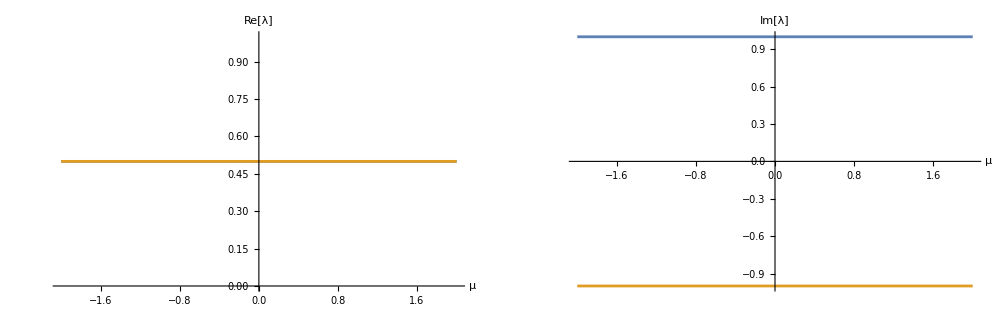

```mathematica
p1 = Plot[{Re[eVal[[1]]],Re[eVal[[2]]]},{μ,-2,2},AxesLabel->{μ,""},PlotLabel->"Re[λ]"];
p2 = Plot[{Im[eVal[[1]]],Im[eVal[[2]]]},{μ,-2,2},AxesLabel->{μ,""},PlotLabel->"Im[λ]"];
Show[GraphicsRow[{p1,p2}],PlotLabel->Style["Eigenvalues of the linearization at (0,0)","Subsubsection"],ImageSize->1000]//Panel
```

## The Phase Plane - Visualizing portions to illustrate a point

### Near the equilibrium point (0,0)

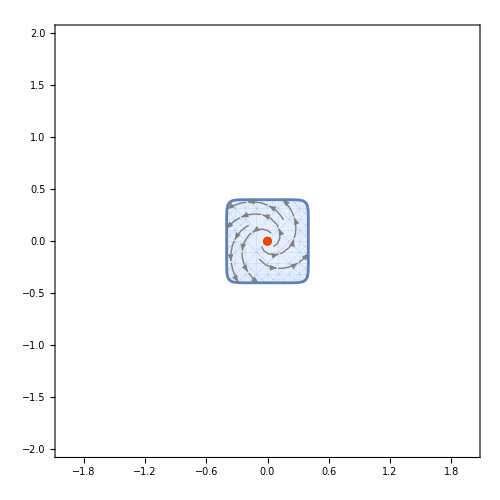

```mathematica
p1 := StreamPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->70,
StreamScale->0.05,
RegionFunction->Function[{x,y,vx,vy,n},x^10+y^10<(.4)^10]]; (*This last part restricts the plotting region*)
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p3]
```

### Away from the equilibrium point

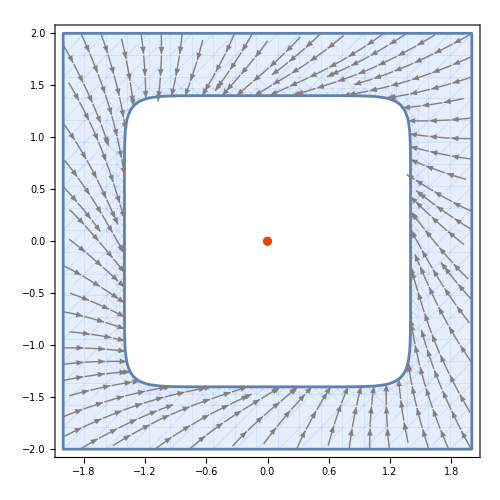

```mathematica
p1 := StreamPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->70,
StreamScale->0.05,RegionFunction->Function[{x,y,vx,vy,n},x^10+y^10>1.4^10]];
p2 := ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->ColorData["SolarColors"][.8]];
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p3]
```

### Viewing Everything

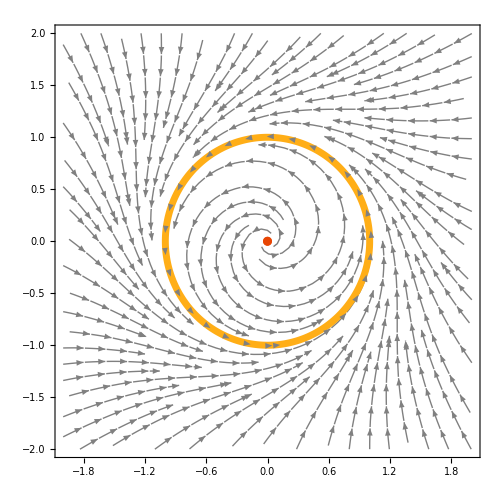

```mathematica
p1 := StreamPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->70,
StreamScale->0.05];
p2 := ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{{ColorData["SolarColors"][.8],Thickness[0.01]}}];
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p2,p3]
```

## Analyzing the System in Polar Coordinates

Let’s define the change of variables given by  where  and

```mathematica
varChange = {x->r Cos[θ], y->r Sin[θ]}
```

Now, we know that   and . This will allow us to determine  and  in a slightly different manner than we did in class.  For example, since , we can use implicit differentiation to determine   or in a more compact form, we have that  or . In the line below, we will simplify this expression for  where we will let  and

```mathematica
rDot = (x f[x,y] + y g[x,y])/r;
rDot = rDot/.varChange//FullSimplify
```

1/2 (r-r^3)

Likewise, since , we have so that  which yields

```mathematica
thetaDot = (g[x,y]x - f[x,y]y)/(x^2 + y^2);
thetaDot = thetaDot/.varChange//FullSimplify
```

-1

Thus, we now know that we have the system  and .  Doing the streamplot in the  plane, we find the following:

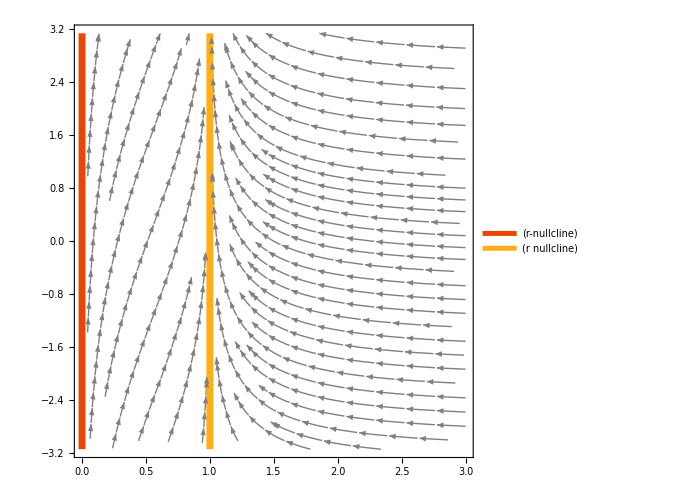

```mathematica
(*Plot the StreamPlot in the r-theta plane*)
p1 = StreamPlot[{rDot,thetaDot},{r,0,3},{θ,-Pi,Pi},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->70,
StreamScale->0.075];
p2 = ParametricPlot[{{0,t},{1,t}},{t,-Pi,Pi},
PlotStyle->{
{ColorData["SolarColors"][.4],Thickness[0.01]},
{ColorData["SolarColors"][.8],Thickness[0.01]}
},
PlotLegends->{
" (r-nullcline)",
" (r nullcline)"
}];
Show[p1,p2,FrameLabel->{"",""}]
```

## Showing the Nullclines in the plane

Here, we will use the command “ContourPlot” in Mathematica with the restrictions that f==0 to give the x-nullclines, and the restriction that g==0 to give the y-nullclines.

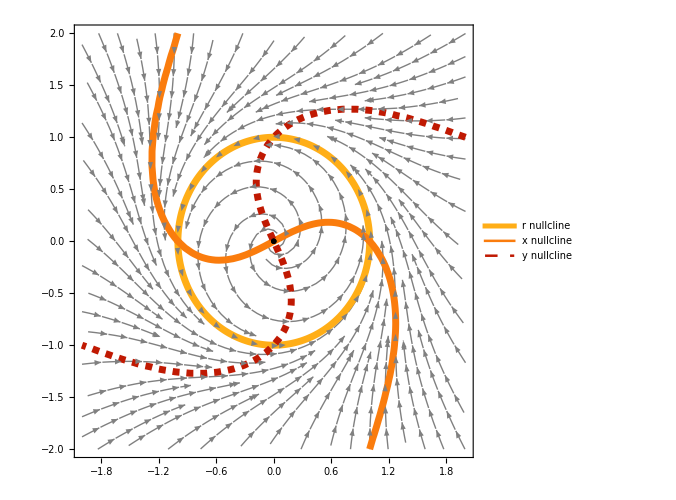

```mathematica
(*Plot the x nullclines and the y nullclines using the "ContourPlot" command to specifically plot the level set where f(x,y) = 0, and g(x,y) = 0.*)
p0:= ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-2,2},{y,-2,2},
ImageSize->300,
ContourStyle->{
{Thickness[.01],ColorData["SolarColors"][.6]},
{Thickness[.01],ColorData["SolarColors"][.2],Dashed}
},
PlotLegends->{
"x nullcline",
"y nullcline"}
]

(*Plot the full stream plot for all x,y values in (-2,2)x(-2,2)*)
p1 := StreamPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2},
ImageSize->300,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->60,
StreamScale->0.05
];

(*Plot the r = 1 nullcline which corresponds to the unit circle*)
p2 := ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},
PlotStyle->{Thickness[.01],ColorData["SolarColors"][.8]},
PlotLegends->{"r nullcline"}
];

(*Plot the equilibrium point (0,0)*)
p3:=ListPlot[{{0,0}},
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black
];

Show[p1,p2,p0,p3,ImageSize->500]
```